```mathematica
SetDirectory[NotebookDirectory[]];
```

## Functions

```mathematica
XYtoList[x_,y_]:=If[Length[x]==Length[y],Table[{x[[i]],y[[i]]},{i,1,Length[x]}]]
listtoXYlist[x_]:=Table[{{x[[i,1]]},x[[i,2]]},{i,1,Length[x]}]
```

```mathematica
Z[s_]:=ElementData[s,"AtomicNumber"]
e[z_]:="Element " <> ToString[ElementData[z,"Abbreviation"]]
e2[z_]:= ToString[ElementData[z,"Abbreviation"]]
A[s_]:=ElementData[s,"AtomicWeight"]
```

## NIST database

Import the f1 & f2 NIST database file (combination of Chantler 1995 and 2000 tables)

```mathematica
NISTdb=Import["f1f2_NIST.dat","Table"]
```

{{//Hydrogen},{//H,,Z=1},{//E[keV],,f1[e/atom],,f2[e/atom],,Î.bc/Ï.81(photo)[cm^2/g],,Ï.83/Ï.81(coh+inc)[cm^2/g],,Î.bc/Ï.81(total)[cm^2/g],,Î»[nm]},{0.01069,0.454682,0.,0.,0.22129,0.22129,0.,116.},{0.0114276,0.39717,0.,0.,0.24489,0.24489,0.,108.5},«40446»,{354.405,92.2078,0.51581,0.2573,0.09355,0.35085,0.2058,0.003498},{378.859,92.1966,0.46523,0.21709,0.08957,0.30666,0.1738,0.003273},{405.,92.1851,0.41966,0.18318,0.08586,0.26904,0.1468,0.003061},{432.945,92.1736,0.37858,0.15459,0.082388,0.23698,0.124,0.002864}}

Deal with formatting of database file

```mathematica
NISTdbseps=DeleteCases[Table[If[StringTake[ToString[NISTdb[[x,1]]],2]=="//",x,0],{x,1,Length[NISTdb]}],0];
```

Function to extract desired column of data

```mathematica
NIST[z_]:=NISTdb[[NISTdbseps[[3*z]]+1;;If[z<92,NISTdbseps[[3*z+1]]-1,-1]]]
```

Make tables of f1, f2 and mu values

```mathematica
NISTf1=Table[XYtoList[NIST[i][[All,1]]*1000,NIST[i][[All,2]]],{i,1,91,1}];
NISTf2=Table[XYtoList[NIST[i][[All,1]]*1000,NIST[i][[All,3]]],{i,1,91,1}];
NISTmu=Table[XYtoList[NIST[i][[All,1]]*1000,NIST[i][[All,4]]],{i,1,91,1}];
```

```mathematica
Manipulate[ListLogLinearPlot[{NISTf1[[i]],NISTf2[[i]]},PlotRange->{All,{-20,100}},PlotLabel->e2[i]<>", f1, f2"],{i,1,91,1}]
```

```mathematica
Manipulate[ListLogLinearPlot[{NISTmu[[i]]},PlotRange->{All,{-20,100}},PlotLabel->e2[i]<>", f1, f2"],{i,1,91,1}]
```

## Henke database

Import the f1 & f2 Henke database file

```mathematica
henkeDB=Import["f1f2_Henke.dat","Table"]
```

{{#F,f1f2_Henke.dat},{#UT,Elastic,Photon-Atom,Scattering,,anomalous,scattering,factors.},{#C,This,file,has,been,created,using,f1f2_Henke.pro,on,Tue,Oct,1,14:33:56,2002},{#C,This,file,belongs,to,the,DABAX,library.,More,information,on},{#C,DABAX,can,be,found,at:},{#C,http://www.esrf.fr/computing/scientific/dabax},«47601»,{27687.3,90.2458,8.11349},{28135.1,90.3582,7.91465},{28590.2,90.4611,7.7198},{29052.6,90.5564,7.52892},{29522.5,90.6621,7.34197},{30000.,90.6603,7.15894}}

Define conversion constant for f2 -> mu

```mathematica
f2Const[i_] := 2*2.8179403267*10^(-15)*4.13566733*10^(-15)*299792458/A[i]*6.0221415*10^(23)*10000
```

Deal with database format and load into a more compact tabulated form (henkeDBT)

```mathematica
henkeDBseps=DeleteCases[Table[If[henkeDB[[x,1]]=="#S",x,0],{x,1,Length[henkeDB]}],0];
henkeDBoffset[input_]:=Max[Table[If[input[[x,1]]=="#UO",x,0],{x,1,Length[input]}],0];
henkeDBoffs=Table[henkeDBoffset[henkeDB[[henkeDBseps[[i]];;henkeDBseps[[i+1]]]]],{i,1,Length[henkeDBseps]-1,1}];
henkeDBT=Table[henkeDB[[henkeDBseps[[i]]+henkeDBoffs[[i]];;henkeDBseps[[i+1]]-1]],{i,1,Length[henkeDBseps]-1,1}];
```

Extract f1 & f2 from henkeDBT and also calculated mu from f2

```mathematica
henkef1=Table[XYtoList[henkeDBT[[i]][[All,1]],henkeDBT[[i]][[All,2]]],{i,1,91,1}];
henkef2=Table[XYtoList[henkeDBT[[i]][[All,1]],henkeDBT[[i]][[All,3]]],{i,1,91,1}];
henkemu=Table[XYtoList[henkeDBT[[i]][[All,1]],f2Const[i]*henkeDBT[[i]][[All,3]]/henkeDBT[[i]][[All,1]]],{i,1,91,1}];
```

```mathematica
Manipulate[ListPlot[{henkef1[[i]],henkef2[[i]]},PlotRange->{All,Automatic},PlotLabel->e2[i]<>", f1, f2"],{i,1,91,1}]
```

```mathematica
Manipulate[ListLinePlot[{henkemu[[i]]},PlotRange->{{0,2000},Automatic},PlotLabel->e2[i]<>", mu"],{i,1,91,1}]
```

## Comparison of Henke and NIST (Chantler 1995 + 2000)

```mathematica
Manipulate[ListLogLinearPlot[{henkef1[[i]],henkef2[[i]],NISTf1[[i]],NISTf2[[i]]},PlotRange->{{0,4000},Automatic},PlotLabel->e2[i]<>", f1, f2"],{i,1,91,1}]
```

```mathematica
Manipulate[ListLogLinearPlot[{NISTmu[[i]],henkemu[[i]]},PlotRange->{{0,4000},{0,50000}},PlotLabel->e2[i]<>", mu"],{i,1,91,1}]
```

## How to access the data

Say I want mu for O and Cu using the NIST database, I would use the following commands

```mathematica
muO = NISTmu[[8]];
muCu = NISTmu[[29]];
```

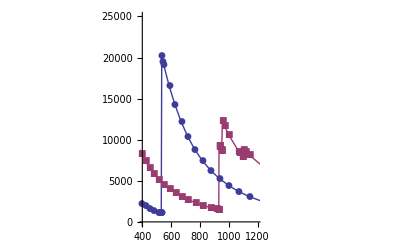

```mathematica
ListLinePlot[{muO,muCu},PlotRange->{{400,1200},{0,25000}},PlotMarkers->Automatic]
```

Say I want interpolated versions of those functions, I would use

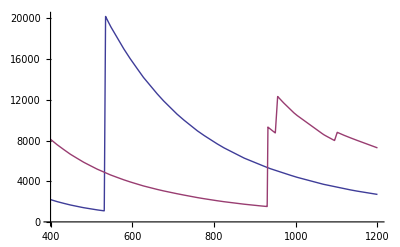

```mathematica
muOInterp=Interpolation[muO,InterpolationOrder->1];
muCuInterp=Interpolation[muCu,InterpolationOrder->1];
Plot[{muOInterp[x],muCuInterp[x]},{x,400,1200}]
```

So now if I want to know muCu (units of cm^2/g) at 900 eV I can ask

```mathematica
muCuInterp[900]
```

1630.71

## Example plots

```mathematica
PlotComparison[x_]:=ListLogLinearPlot[{henkef1[[x]],henkef2[[x]],NISTf1[[x]],NISTf2[[x]]},PlotRange->{{30,30000},Automatic},PlotLabel->e2[x]<>", f1, f2",Joined->True]
```

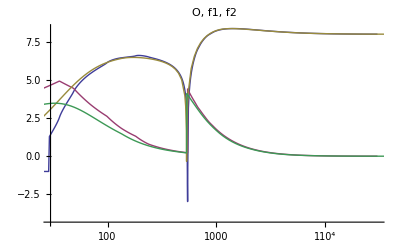

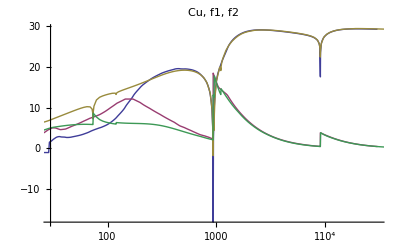

```mathematica
PlotComparison[Z["O"]]
PlotComparison[Z["Cu"]]
```